## Electric Field Around Box

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
NotebookDirectory[]
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis\ComputationalPhysicsFinalProj\

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis\ComputationalPhysicsFinalProj

#### Creating the Box

Importing file with box, the filenames are called smallDenseBoxS and then the ratio of the number of points per side to the original box model

```mathematica
box = Import["smallDenseBox.csv"];
```

The bounding region around all the different boxes with different point densities should be close to Cuboid[{-0.4, -0.4, -0.4},{0.4, 0.4, 0.4}]. If the bounding region is exactly that then the box is a cube. However, given point densities it is often impossible to create a cube due to different lattices on different sides, however this is as close to a cube as we could get the boxes

```mathematica
BoundingRegion[box]
```

Cuboid[{-0.4,-0.389711,-0.4465},{0.4,0.389709,0.4205}]

```mathematica
Volume[BoundingRegion[box]]
```

0.540606

```mathematica
boxFull = DeleteDuplicates[box, EuclideanDistance[#1,#2]< .01 &];
```

```mathematica
Length[boxFull]
```

1578

```mathematica
c = RegionCentroid[Point[boxFull]]
```

{0.,5.79217×10^-9,-0.0133036}

```mathematica
boxCentered = #-c &/@ boxFull;
```

```mathematica
Length[boxCentered]
```

1578

#### Eliminating edges

Because in order to calculate the E-field, we must use the normal vector to each point charge, we do not use the point charges on the edges of the box as they do not have a well defined normal vector. Here we eliminate all points from our list that are on two sides and thus have two well defined coordinates.

```mathematica
Edges = {}
Sides = {}

If[(((#[[1]] == SortBy[boxCentered, #[[1]]&][[-1]][[1]]
||#[[1]]==SortBy[boxCentered, #[[1]]&][[1]][[1]]) 
&& 
(#[[2]]==SortBy[boxCentered, #[[2]]&][[-1]][[2]]
||#[[2]]==SortBy[boxCentered, #[[2]]&][[1]][[2]])) 

|| ((#[[1]] == SortBy[boxCentered, #[[1]]&][[-1]][[1]]
||#[[1]]==SortBy[boxCentered, #[[1]]&][[1]][[1]])
&&
(#[[3]]==SortBy[boxCentered, #[[3]]&][[1]][[3]]
||#[[3]]==SortBy[boxCentered, #[[3]]&][[-1]][[3]]))
 
||((#[[3]]==SortBy[boxCentered, #[[3]]&][[1]][[3]]
||#[[3]]==SortBy[boxCentered, #[[3]]&][[-1]][[3]]) 
&&
(#[[2]]==SortBy[boxCentered, #[[2]]&][[-1]][[2]]
||#[[2]]==SortBy[boxCentered, #[[2]]&][[1]][[2]]))), 
AppendTo[Edges, #], AppendTo[Sides, #]]&/@boxCentered;
```

{}

{}

```mathematica
Length[Sides]
```

1457

```mathematica
ListPointPlot3D[Sides, AxesLabel->{x,y, z}, PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
Graphics3D[BoundingRegion[Sides]]
```

-Graphics3D-

```mathematica
Show[%,%%]
```

-Graphics3D-

### Finding the Charges

```mathematica
length = Length[Sides]
```

1457

#### We divide out all the 6 sides, and find the voronoi area associated with each point on each side

First step: Separate the Sides array into separate sides. This allows for us to calculate the voronoi area (area surrounding each point) around each point

```mathematica
Side1 = {}
filter[i_] := If[Sides[[i]][[3]]>BoundingRegion[Sides][[2]][[3]]-.00001, AppendTo[Side1, Sides[[i]]]]
filter[#]&/@ Range[Length[Sides]];
Side1;
Length[Side1]
```

{}

264

```mathematica
Side2 = {}
filter[i_] := If[Sides[[i]][[3]]<BoundingRegion[Sides][[1]][[3]]+.000001, AppendTo[Side2, Sides[[i]]]]
filter[#]&/@ Range[Length[Sides]];
Side2;
Length[Side2]
```

{}

264

```mathematica
Side3 = {}
filter[i_] := If[Sides[[i]][[1]]<BoundingRegion[Sides][[1]][[1]] +.00001, AppendTo[Side3, Sides[[i]]]]
filter[#]&/@ Range[Length[Sides]];
Length[Side3]
```

{}

162

```mathematica
Side4 = {}
filter[i_] := If[Sides[[i]][[1]]>BoundingRegion[Sides][[2]][[1]] -.00001, AppendTo[Side4, Sides[[i]]]]
filter[#]&/@ Range[Length[Sides]];
Length[Side4]
```

{}

162

```mathematica
Side5 = {}
filter[i_] := If[Sides[[i]][[2]]<BoundingRegion[Sides][[1]][[2]] +.00001, AppendTo[Side5, Sides[[i]]]]
filter[#]&/@ Range[Length[Sides]];
Length[Side5]
```

{}

310

```mathematica
Side6 = {}
filter[i_] := If[Sides[[i]][[2]]>BoundingRegion[Sides][[2]][[2]] -.00001, AppendTo[Side6, Sides[[i]]]]
filter[#]&/@ Range[Length[Sides]];
Length[Side6]
```

{}

295

#### Assigning areas to each point

Because the function VoronoiMesh assigns areas to points but does not preserve their order, we have to reorder “Sides” so that we know which area is associated with which point. After these next steps, the end result is an array of areas and an array of points such that the i’th point has an area associated with it equal to the i’th element of the area array.

```mathematica
vor= VoronoiMesh[#[[{1,3}]] &/@Side6, {{BoundingRegion[Sides][[1]][[1]],BoundingRegion[Sides][[2]][[1]]},{BoundingRegion[Sides][[1]][[3]], BoundingRegion[Sides][[2]][[3]]}}];
side6 = #[[{1,3}]] &/@Side6;
cellSite[p_,reg_]:=With[{rm=RegionMember[reg]},{Point@Flatten@Pick[p,rm[p]],reg}]
cs=cellSite[side6,#]&/@MeshPrimitives[vor, 2];
areas6=Area[#[[2]]]&/@ %;
```

```mathematica
newSide6 = {#[[1]][[1]][[1]], BoundingRegion[Sides][[2]][[2]] ,#[[1]][[1]][[2]]}&/@cs;
```

```mathematica
vor= VoronoiMesh[#[[{1,3}]] &/@Side5, {{BoundingRegion[Sides][[1]][[1]],BoundingRegion[Sides][[2]][[1]]},{BoundingRegion[Sides][[1]][[3]], BoundingRegion[Sides][[2]][[3]]}}];
side5 = #[[{1,3}]] &/@Side5;
cellSite[p_,reg_]:=With[{rm=RegionMember[reg]},{Point@Flatten@Pick[p,rm[p]],reg}]
cs=cellSite[side5,#]&/@MeshPrimitives[vor, 2];
areas5=Area[#[[2]]]&/@ %;
```

```mathematica
newSide5 = {#[[1]][[1]][[1]], BoundingRegion[Sides][[1]][[2]] ,#[[1]][[1]][[2]]}&/@cs;
```

```mathematica
ListPointPlot3D[Side4]
```

-Graphics3D-

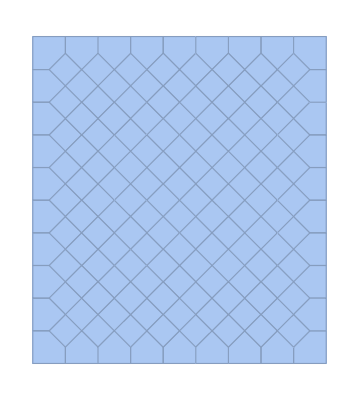

```mathematica
vor = VoronoiMesh[#[[2;;3]] &/@Side4, {{BoundingRegion[boxCentered][[1]][[2]], BoundingRegion[boxCentered][[2]][[2]]}, {BoundingRegion[boxCentered][[1]][[3]], BoundingRegion[boxCentered][[2]][[3]]}}]
side4 = #[[2;;3]] &/@Side4;
cellSite[p_,reg_]:=With[{rm=RegionMember[reg]},{Point@Flatten@Pick[p,rm[p]],reg}]
cs=cellSite[side4,#]&/@MeshPrimitives[vor, 2];
areas4=Area[#[[2]]]&/@ %;
```

```mathematica
newSide4 = { BoundingRegion[Sides][[2]][[1]],#[[1]][[1]][[1]] ,#[[1]][[1]][[2]]}&/@cs;
```

```mathematica
vor = VoronoiMesh[#[[2;;3]] &/@Side3, {{BoundingRegion[Sides][[1]][[2]], BoundingRegion[Sides][[2]][[2]]}, {BoundingRegion[Sides][[1]][[3]], BoundingRegion[Sides][[2]][[3]]}}]
side3 = #[[2;;3]] &/@ Side3;
cellSite[p_,reg_]:=With[{rm=RegionMember[reg]},{Point@Flatten@Pick[p,rm[p]],reg}]
cs=cellSite[side3,#]&/@MeshPrimitives[vor, 2];
areas3=Area[#[[2]]]&/@ %;
```

-Graphics-

```mathematica
newSide3 = {BoundingRegion[Sides][[1]][[1]],#[[1]][[1]][[1]] ,#[[1]][[1]][[2]]}&/@cs;
```

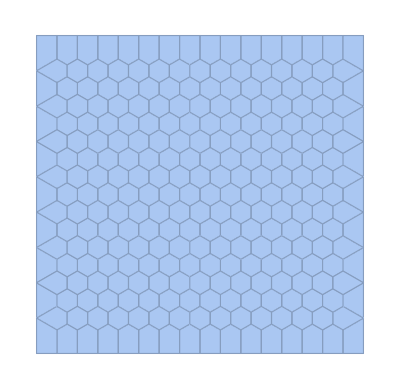

```mathematica
vor = VoronoiMesh[#[[1;;2]] &/@Side2, {{BoundingRegion[Sides][[1]][[1]],BoundingRegion[Sides][[2]][[1]]},{BoundingRegion[Sides][[1]][[2]], BoundingRegion[Sides][[2]][[2]]}}]
side2 = #[[1;;2]] &/@Side2;
cellSite[p_,reg_]:=With[{rm=RegionMember[reg]},{Point@Flatten@Pick[p,rm[p]],reg}]
cs=cellSite[side2,#]&/@MeshPrimitives[vor, 2];
areas2=Area[#[[2]]]&/@ %;
```

```mathematica
newSide2 = {#[[1]][[1]][[1]] ,#[[1]][[1]][[2]], BoundingRegion[Sides][[1]][[3]]}&/@cs;
```

```mathematica
vor = VoronoiMesh[#[[1;;2]] &/@Side1, {{BoundingRegion[Sides][[1]][[1]],BoundingRegion[Sides][[2]][[1]]},{BoundingRegion[Sides][[1]][[2]], BoundingRegion[Sides][[2]][[2]]}}];
side1 = #[[1;;2]] &/@Side1;
cellSite[p_,reg_]:=With[{rm=RegionMember[reg]},{Point@Flatten@Pick[p,rm[p]],reg}]
cs=cellSite[side1,#]&/@MeshPrimitives[vor, 2];
areas1=Area[#[[2]]]&/@ %;
```

```mathematica
newSide1 = {#[[1]][[1]][[1]] ,#[[1]][[1]][[2]], BoundingRegion[Sides][[2]][[3]]}&/@cs;
```

```mathematica
Clear[DensityArray]
```

```mathematica
DensityArray = Join[areas1,areas2, areas3, areas4, areas5, areas6];
newSides = Join[newSide1, newSide2, newSide3, newSide4, newSide5, newSide6];
```

```mathematica
Length[newSide1]
Length[newSide2]
Length[newSide3]
Length[newSide4]
Length[newSide5]
Length[newSide6]
```

264

264

162

162

310

295

```mathematica
Length[DensityArray]
```

1457

```mathematica
density[i_]:= DensityArray[[i]]
```

```mathematica
BoundingRegion[newSides]
```

Cuboid[{-0.4,-0.389711,-0.433196},{0.4,0.389709,0.433804}]

#### Finding density per side

```mathematica
(*density1 = Area[BoundingRegion[#[[1;;2]]&/@Sides[[1;;246]], "MinRectangle"]]/Length[Sides[[1;;246]]]*)
density1 = Area[BoundingRegion[#[[1;;2]]&/@Side1, "MinRectangle"]]/Length[Side1]
```

0.00196824

```mathematica
(*density2 = Area[BoundingRegion[#[[1;;2]]&/@Sides[[247;;492]], "MinRectangle"]]/Length[Sides[[247;;492]]]*)
density2 = Area[BoundingRegion[#[[1;;2]]&/@Side2, "MinRectangle"]]/Length[Side2]
```

0.00196824

```mathematica
(*density3 = Area[BoundingRegion[#[[2;;3]]&/@Sides[[493;;534]], "MinRectangle"]]/Length[Sides[[493;;534]]]*)
density3 = Area[BoundingRegion[#[[2;;3]]&/@Side3, "MinRectangle"]]/Length[Side3]
```

0.00333332

```mathematica
density4 = Area[BoundingRegion[#[[2;;3]]&/@Side4, "MinRectangle"]]/Length[Side4]
```

0.00333332

```mathematica
density5 = Area[BoundingRegion[{#[[1]],#[[3]]}&/@Side5, "MinRectangle"]]/Length[Side5]
```

0.00199048

```mathematica
density6 = Area[BoundingRegion[{#[[1]],#[[3]]}&/@Side6, "MinRectangle"]]/Length[Side6]
```

0.00198158

#### Functions necessary for calculating the matrix. The normal and density functions depend on the side

coulombs law (for effect of other charges)

```mathematica
R[r_,j_]:=(r- newSides[[j]])/(Norm[r- newSides[[j]]])^3
```

```mathematica
BoundingRegion[boxCentered]
```

Cuboid[{-0.4,-0.389711,-0.433196},{0.4,0.389709,0.433804}]

calculating normal component at each point

```mathematica
normal[r_] := If[r[[3]] > BoundingRegion[newSides][[2]][[3]]-.00001, {0,0,1}, 
If[r[[3]] < BoundingRegion[newSides][[1]][[3]] +.00001, {0,0,-1}, 
If[r[[1]] > BoundingRegion[newSides][[2]][[1]] -.00001, {1,0,0}, 
If[r[[1]] < BoundingRegion[newSides][[1]][[1]] +.00001,{-1,0,0}, 
If[r[[2]]> BoundingRegion[newSides][[2]][[2]] -.00001, {0,1,0}, {0,-1,0}]]]]]
```

```mathematica
Max[Norm[normal[newSides[[#]]]*density[#]&/@Range[length]]  ]
Arrow[{newSides[[#]], newSides[[#]]+(10/%)normal[newSides[[#]]]*density[#]}]&/@Range[length];
(*Graphics3D[{Arrowheads[.01],%, {Opacity[.8], Sphere[{0,0,0}, .99]}}, Axes->True, AxesLabel->{"x", "y", "z"}]*)
Graphics3D[{Arrowheads[.01],%, {Opacity[1], BoundingRegion[newSides]}}, Axes->True, AxesLabel->{"x", "y", "z"}]
```

0.0765557

-Graphics3D-

Calculating density

```mathematica
density[i_]:= DensityArray[[i]]
```

#### Creating a matrix to calculate charges

This matrix multiplied by a list of charges should produce a set of vectors whose normal components are equal and opposite to the normal component of Ezero. This matrix inverted allows to calculate the depolarization field

```mathematica
EMatrix = -Table[If[i==j, (2Pi/density[i]), (R[newSides[[i]],j].normal[newSides[[i]]])], {i, length},{j, length}];
```

```mathematica
i
```

1252

```mathematica
MatrixForm[EMatrix[[1;;20,1;;20]]]
```

(-1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1934.78 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1741.29 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2176.47 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2176.47 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2176.59 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2176.59 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -2176.47)

```mathematica
Dimensions[EMatrix]
```

{1457,1457}

Because we need Ezero at each stokeslet, we need to create an array of Ezeros. To accurately compare with Koolstra data Ezero has to be -2/3

```mathematica
Ezero = {-2/3,0,0}
EzeroTable = Table[Flatten[Ezero], length];
```

{-2/3,0,0}

```mathematica
normalOfField=Table[EzeroTable[[i]].normal[newSides[[i]]], {i, length}];
```

```mathematica
Q= LinearSolve[EMatrix, normalOfField];
```

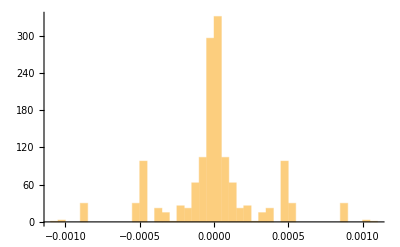

```mathematica
Histogram[Q, PlotRange->All]
```

#### Calculating E-Field

```mathematica
Ezero
```

{-2/3,0,0}

```mathematica
EField[r_] := Sum[If[r ==newSides[[j]], 2Pi/density[j]*normal[newSides[[j]]]*Q[[j]], R[r, j]*Q[[j]]], {j,length}]+Ezero
```

```mathematica
DumpSave["smallDenseCubeField.mx", "Global`"]
```

{Global`}

```mathematica
StreamPlot[(EField[{x,y,0}][[1;;2]]), {x,-1.5, 1.5}, {y,-1, 1}]
```

This file culminates in creating a field around a cube. It saves the contents of this notebook which can then be used in a different one later on for comparison with koolstra data. In this portion of the project I used matrix inversion and boundary conditions in order to determine the EField at each point